Power::infy: Infinite expression 1/0. encountered.

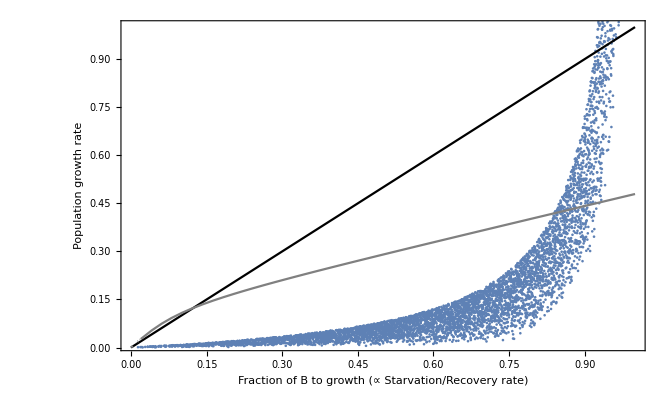

```mathematica
SppData = Table[
β=RandomReal[{0.5,1}];
(*b = RandomReal[{0.000001,0.00001}];*)
b = 0.08; (*RandomReal[{0.00002,1}];*)
ϵ=RandomReal[{1,20}];
γ0 = x;
η = 1;
{η*γ0,N[ Log[ϵ]/(1/(b*(1-β))*Log[γ0/(1-ϵ^(1-β)*(1-γ0))])]},
{x,0.0001,1,0.0001}];
Colors = {Black,Transparent,Transparent,Gray};
Show[{
ListPlot[SppData,PlotRange->{{0,1},{0.01,1}},Frame->True,FrameLabel->{"Fraction of B to growth (∝ Starvation/Recovery rate)","Population growth rate"},PlotStyle->ColorData[97,1]],
Table[Plot[λ/.Hsp[[x]],{η,0,1},PlotRange->{0,1},Frame->True,FrameLabel->{"η","λ"},PlotStyle->Colors[[x]]],{x,1,4}]
}]
```

```mathematica
Manipulate[
Show[{
LogLogPlot[c*M^(-1/4),{M,0.001,10000},PlotRange->All],
LogLogPlot[1/Log[M],{M,0.001,10000}]
}],
{c,0,10}]
```

```mathematica
Solve[c*1/Log[x] == x^(-β),x]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→(-ProductLog[-c β]/(c β))^(1/β)}}

```mathematica
Assuming[
```

```mathematica
Reduce[(-ProductLog[-c β]/(c β))^(1/β)≥0,c]
```

$Aborted